# WKB Theory

```mathematica
Clear[y,x,ϵ,δ,S0,S1,S2]
```

### Expansion

Compute the ODE for boundary conditions at  and

```mathematica
Clear[ϵ,y]
a = 0;
b = Pi/2; 

ODEi = ϵ*y''[x] - (1/(4 + Sin[x]))*y'[x] + y[x]
BCa = 1; (*Plug in value at a*)
BCb = 1; (*Plug in value at b*)
```

y[x]-y'[x]/(4+Sin[x])+ϵ y''[x]

Assume the solution takes the form

```mathematica
S[x_] = S0[x] + δ*S1[x]; (*+ δ^2*S2[x];*)
y[x_] = Exp[S[x]/δ]
```

ⅇ^((S0[x]+δ S1[x])/δ)

### Dominant Balance

Then the ODE is of the form

```mathematica
ODE = Simplify[ODEi / y[x]]
```

1/(δ^2 (4+Sin[x]))(ϵ (4+Sin[x]) S0'[x]^2+δ S0'[x] (-1+2 ϵ (4+Sin[x]) S1'[x])+δ (-δ S1'[x]+δ ϵ (4+Sin[x]) S1'[x]^2+(4+Sin[x]) (δ+ϵ S0''[x]+δ ϵ S1''[x])))

Then to find the dommy value, we look at

```mathematica
Collect [ODE,δ]
```

(ϵ S0'[x]^2)/δ^2+(S0'[x] (-1+2 ϵ (4+Sin[x]) S1'[x])+ϵ (4+Sin[x]) S0''[x])/(δ (4+Sin[x]))+(4+Sin[x]-S1'[x]+ϵ (4+Sin[x]) S1'[x]^2+ϵ (4+Sin[x]) S1''[x])/(4+Sin[x])

Find the lowest power of  not attached to ϵ and set it equal to the lowest power of δ attached to ϵ. Then the dommy value is

```mathematica
δ = ϵ;
```

### Solve for S

Plug in to the ODE and collecting terms we get

```mathematica
ODEs = Simplify[Coefficient[ODE,ϵ,{-1,0,1}]];

MatrixForm[ODEs]
```

(S0'[x] (-1/(4+Sin[x])+S0'[x])
1+(-1/(4+Sin[x])+2 S0'[x]) S1'[x]+S0''[x]
S1'[x]^2+S1''[x])

Solve the leading order problem. We can set the integration consistent equal to zero since it will be accounted for at the end

```mathematica
S0sols = DSolve[ODEs[[1]]==0,S0[x],x] /. C[1] -> 0
Simplify[DSolve[-1/(4+Sin[x])+S0'[x] == 0,S0[x],x]]
```

{{S0[x]→0},{S0[x]→(2 ArcTan[(1+4 Tan[x/2])/(√15)])/(√15)}}

{{S0[x]→(2 ArcTan[(1+4 Tan[x/2])/(√15)])/(√15)+C[1]}}

This gives us two cases (hopefully)

#### Case 1

Using the first solution S_(0_x)=0 (the outer problem)

```mathematica
S10[x_] = S0[x] /. S0sols[[1]];
```

Plugging this solution into the next order term

```mathematica
ODEs[[2]] /. S0 -> S10
```

1-S1'[x]/(4+Sin[x])

And solving this gives

```mathematica
sol = DSolve[(ODEs[[2]] /. {S0 -> S10}) == 0,S1[x],x] /. C[1] -> 0;
S11[x_] = S1[x] /. sol[[1]]
```

4 x-Cos[x]

Plugging this into the solution for

```mathematica
y1[x_] = Simplify[y[x] /. {S0 -> S10, S1 -> S11}]
```

ⅇ^(4 x-Cos[x])

#### Case 2

Now using the second solution for S2

```mathematica
S20[x_] = S0[x] /. S0sols[[2]];
```

Plugging this solution into the next order term

```mathematica
ODEs[[2]] /. S0 -> S20
```

1-(16 Sec[x/2]^4 (1+4 Tan[x/2]))/(225 (1+1/15 (1+4 Tan[x/2])^2)^2)+(4 Sec[x/2]^2 Tan[x/2])/(15 (1+1/15 (1+4 Tan[x/2])^2))+(-1/(4+Sin[x])+(8 Sec[x/2]^2)/(15 (1+1/15 (1+4 Tan[x/2])^2))) S1'[x]

And solving this gives

```mathematica
sol = DSolve[(ODEs[[2]] /. {S0 -> S20}) == 0,S1[x],x] /. C[1] -> 0;
S21[x_] = S1[x] /. sol[[1]]
```

-4 x+Cos[x]+Log[4+Sin[x]]

Plugging this into the solution for

```mathematica
y2[x_] = Simplify[y[x] /. {S0 -> S20, S1 -> S21}]
```

ⅇ^(-4 x+(2 ArcTan[(1+4 Tan[x/2])/(√15)])/(√15 ϵ)+Cos[x]) (4+Sin[x])

### Enforce the Initial Conditions

The solution of WKB theory is of the form .

```mathematica
Clear[c,d]
yui[x_] = c*y1[x] + d*y2[x]
```

c ⅇ^(4 x-Cos[x])+d ⅇ^(-4 x+(2 ArcTan[(1+4 Tan[x/2])/(√15)])/(√15 ϵ)+Cos[x]) (4+Sin[x])

We can enforce the initial conditions to solve for  and d.

```mathematica
coeffs = Simplify[Solve[{yui[a] == BCa, yui[b] == BCb}, {c,d}]]
```

{{c→(ⅇ (-5 ⅇ^((2 ArcTan[√(5/3)])/(√15 ϵ))+4 ⅇ^(1+2 π+(2 ArcTan[1/(√15)])/(√15 ϵ))))/(-5 ⅇ^((2 ArcTan[√(5/3)])/(√15 ϵ))+4 ⅇ^(2+4 π+(2 ArcTan[1/(√15)])/(√15 ϵ))),d→(ⅇ^(2 π) (-1+ⅇ^(1+2 π)))/(-5 ⅇ^((2 ArcTan[√(5/3)])/(√15 ϵ))+4 ⅇ^(2+4 π+(2 ArcTan[1/(√15)])/(√15 ϵ)))}}

Thus the solution is

```mathematica
yu[x_,ϵ_] = yui[x] /. coeffs[[1]]
```

(ⅇ^(1+4 x-Cos[x]) (-5 ⅇ^((2 ArcTan[√(5/3)])/(√15 ϵ))+4 ⅇ^(1+2 π+(2 ArcTan[1/(√15)])/(√15 ϵ))))/(-5 ⅇ^((2 ArcTan[√(5/3)])/(√15 ϵ))+4 ⅇ^(2+4 π+(2 ArcTan[1/(√15)])/(√15 ϵ)))+(ⅇ^(2 π-4 x+(2 ArcTan[(1+4 Tan[x/2])/(√15)])/(√15 ϵ)+Cos[x]) (-1+ⅇ^(1+2 π)) (4+Sin[x]))/(-5 ⅇ^((2 ArcTan[√(5/3)])/(√15 ϵ))+4 ⅇ^(2+4 π+(2 ArcTan[1/(√15)])/(√15 ϵ)))

### Overkill Plot

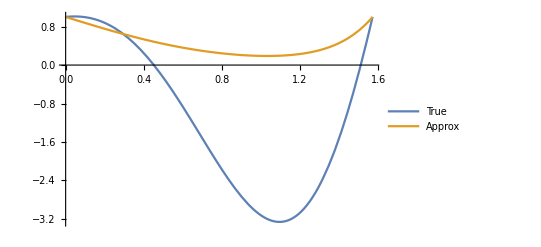

```mathematica
Clear[y,ϵ]
ϵ = 0.1;
sol = NDSolve[{ODEi==0, y[a] == BCa, y[b] == BCb},y[x],x];
num[x_] := Evaluate[y[x] /. sol[[1]]];
Plot[{num[x],yu[x,ϵ]},{x,a,b},PlotLegends->{"True","Approx"}]
Clear[ϵ]
```